# Governing equations of electrochemical network model

#### Abhishek Sharma Cronin Lab University of Glasgow

Please note that some variable names might be different from the description in the manuscript and SI.

All the governing equations for electrochemical kinetics combined with Kirchhoff’s Laws are given by,
All the currents and potentials are indexed as <i>s<j>
All the currents are going in the outward directions

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[Symbol["V"<>indexStr][t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa n F ηm)/(R T)]-Exp[-(αc n F ηm)/(R T)])/.ηm-> Evaluate[Symbol["V"<>indexStr][t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];
eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕPW1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕPS"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕPE"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕPN"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

The governing equations at a single electrode-electrolyte pair :
1. Current conservation (one equation)
2. Butler Volmer Kinetics (one equation)
3. Kirchhoff’s Potential equations (five equations)

```mathematica
TableForm@Flatten@eqns[2,t][[All,1]]/.E0->0
```

i1s1E[t]+i1s1N[t]+i1s1S[t]+i1s1W[t]==iEL1s1[t]
iEL1s1[t]==AreaEL (ⅇ^((F n αa (V1s1[t]-ϕ1s1[t]))/(R T))-ⅇ^(-(F n αc (V1s1[t]-ϕ1s1[t]))/(R T))) i0+AreaEL Cdl (V1s1'[t]-ϕ1s1'[t])
ϕ1s1[t]-ϕP1s1[t]==RBulkA iEL1s1[t]
ϕP1s1[t]-ϕPN1s1[t]==RBulkB i1s1N[t]
ϕP1s1[t]-ϕPE1s1[t]==RBulkB i1s1E[t]
ϕP1s1[t]-ϕPS1s1[t]==RBulkB i1s1S[t]
ϕP1s1[t]-ϕPW1s1[t]==RBulkB i1s1W[t]
i1s2E[t]+i1s2N[t]+i1s2S[t]+i1s2W[t]==iEL1s2[t]
iEL1s2[t]==AreaEL (ⅇ^((F n αa (V1s2[t]-ϕ1s2[t]))/(R T))-ⅇ^(-(F n αc (V1s2[t]-ϕ1s2[t]))/(R T))) i0+AreaEL Cdl (V1s2'[t]-ϕ1s2'[t])
ϕ1s2[t]-ϕP1s2[t]==RBulkA iEL1s2[t]
ϕP1s2[t]-ϕPN1s2[t]==RBulkB i1s2N[t]
ϕP1s2[t]-ϕPE1s2[t]==RBulkB i1s2E[t]
ϕP1s2[t]-ϕPS1s2[t]==RBulkB i1s2S[t]
ϕP1s2[t]-ϕPW1s2[t]==RBulkB i1s2W[t]
i2s1E[t]+i2s1N[t]+i2s1S[t]+i2s1W[t]==iEL2s1[t]
iEL2s1[t]==AreaEL (ⅇ^((F n αa (V2s1[t]-ϕ2s1[t]))/(R T))-ⅇ^(-(F n αc (V2s1[t]-ϕ2s1[t]))/(R T))) i0+AreaEL Cdl (V2s1'[t]-ϕ2s1'[t])
ϕ2s1[t]-ϕP2s1[t]==RBulkA iEL2s1[t]
ϕP2s1[t]-ϕPN2s1[t]==RBulkB i2s1N[t]
ϕP2s1[t]-ϕPE2s1[t]==RBulkB i2s1E[t]
ϕP2s1[t]-ϕPS2s1[t]==RBulkB i2s1S[t]
ϕP2s1[t]-ϕPW2s1[t]==RBulkB i2s1W[t]
i2s2E[t]+i2s2N[t]+i2s2S[t]+i2s2W[t]==iEL2s2[t]
iEL2s2[t]==AreaEL (ⅇ^((F n αa (V2s2[t]-ϕ2s2[t]))/(R T))-ⅇ^(-(F n αc (V2s2[t]-ϕ2s2[t]))/(R T))) i0+AreaEL Cdl (V2s2'[t]-ϕ2s2'[t])
ϕ2s2[t]-ϕP2s2[t]==RBulkA iEL2s2[t]
ϕP2s2[t]-ϕPN2s2[t]==RBulkB i2s2N[t]
ϕP2s2[t]-ϕPE2s2[t]==RBulkB i2s2E[t]
ϕP2s2[t]-ϕPS2s2[t]==RBulkB i2s2S[t]
ϕP2s2[t]-ϕPW2s2[t]==RBulkB i2s2W[t]

The governing equations at connecting the electrode-electrolyte pairs
1. Current conservation (four equations for two electrodes, non boundary)
2. Kirchhoff’s Potential equations  (two equations)

```mathematica
TableForm@Flatten@eqnsCon[2][[All,1]]
```

iCN1s1[t]==i1s1N[t]
iCN1s1[t]==-i1s2S[t]
iCE1s1[t]==i1s1E[t]
iCE1s1[t]==-i2s1W[t]
ϕPN1s1[t]-ϕPS1s2[t]==RConn iCN1s1[t]
ϕPE1s1[t]-ϕPW2s1[t]==RConn iCE1s1[t]

The governing equations at the boundaries and rest of the electrode-electrolyte pairs, all the potential at the edges are considered as 0.
1. Current conservation (twelve equations, four equations for rest of the two electrodes and eight equations for boundaries)
2. Kirchhoff’s Potential equations  (ten  equations)

```mathematica
TableForm@Flatten@eqnsEndCon[2][[1]]
```

iCW1s1[t]==i1s1W[t]
iCW1s2[t]==i1s2W[t]
ϕPW1s1[t]==RConn i1s1W[t]
ϕPW1s2[t]==RConn i1s2W[t]
iCS1s1[t]==i1s1S[t]
iCS2s1[t]==i2s1S[t]
ϕPS1s1[t]==RConn i1s1S[t]
ϕPS2s1[t]==RConn i2s1S[t]
iCE2s1[t]==i2s1E[t]
iCE2s2[t]==i2s2E[t]
ϕPE2s1[t]==RConn i2s1E[t]
ϕPE2s2[t]==RConn i2s2E[t]
iCN2s1[t]==i2s1N[t]
iCN2s1[t]==-i2s2S[t]
ϕPN2s1[t]-ϕPS2s2[t]==RConn i2s1N[t]
iCN1s2[t]==i1s2N[t]
iCN2s2[t]==i2s2N[t]
ϕPN1s2[t]==RConn i1s2N[t]
ϕPN2s2[t]==RConn i2s2N[t]
iCE1s2[t]==i1s2E[t]
iCE1s2[t]==-i2s2W[t]
ϕPE1s2[t]-ϕPW2s2[t]==RConn i1s2E[t]

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ])
```

```mathematica
indexStr="pq"; (* Setting arbitirary index *)
```

```mathematica
fVShift[{V1,V2},{λ,t0},t]
```

V1+(-V1+V2) (1/2+ArcTan[(t-t0)/λ]/π)

```mathematica
D[fVShift[{V1,V2},{λ,t0},t],t]//FullSimplify
```

((-V1+V2) λ)/(π ((t-t0)^2+λ^2))

```mathematica
Symbol["iEL"<>indexStr][t]==(AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa n F ηm)/(R T)]-Exp[-(αc n F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]]/.E0->0)
```

iELpq[t]==AreaEL (ⅇ^((F n αa (Vipq+(Vfpq-Vipq) (1/2+ArcTan[(t-tS)/λ]/π)-ϕpq[t]))/(R T))-ⅇ^(-(F n αc (Vipq+(Vfpq-Vipq) (1/2+ArcTan[(t-tS)/λ]/π)-ϕpq[t]))/(R T))) i0+AreaEL Cdl ((Vfpq-Vipq)/(π (1+(t-tS)^2/λ^2) λ)-ϕpq'[t])

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/

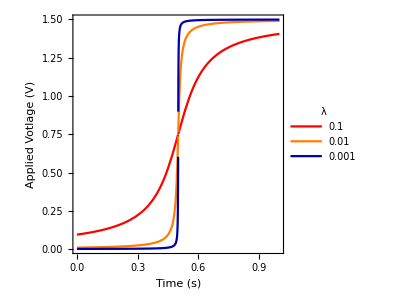

```mathematica
out=Plot[Evaluate[fVShift[{0,1.5},{#,0.5},t]&/@{0.1,0.01,0.001}],{t,0,1},PlotStyle->{Red,Orange,Darker@Blue},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends->Placed[LineLegend[{"0.1","0.01","0.001"},LegendLabel->"λ",Spacings->0.2,LegendFunction->"Panel"],{0.8,0.2}],FrameLabel-> {"Time (s)","Applied Votlage (V)"},AspectRatio->1,Frame->True,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"PotentialStepFunction.png",out,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/PotentialStepFunction.png